Partner potential to symmetric well placed with endpoints at (±a)/2, where a=π*ℏ/mc, and s=x*π/a, V_0=-1/2

```mathematica
V[s_]:=(Sec[s]^2-1/2);
ds=π/n-0.00002;
n=551;s=Table[-π/2.+ds*i,{i,n}];
one[n_,d_]:=DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=(one[n,-1]+10one[n,0]+one[n,1])/12.;
A=(one[n,-1]-2one[n,0]+one[n,1])/ds^2;
KE=-Inverse[B].A/2;
H=KE+DiagonalMatrix[V[s]];
{eval,evec}=Eigensystem[H];
```

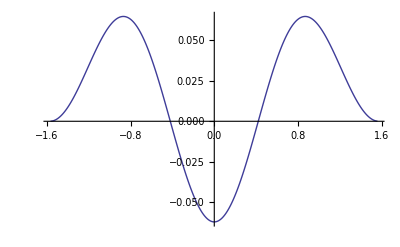

```mathematica
f[n_]:=s[[n]];
data[m_]:=Table[{f[j],evec[[-m]][[j]]},{j,1,n}];
ListPlot[data[3],PlotJoined->True,PlotRange->All]
```

```mathematica
eval=eval//Sort;
```

```mathematica
eval[[;;20]]
```

{1.5,4.,7.5,12.,17.5,24.,31.5001,40.0001,49.5001,60.0002,71.5003,84.0004,97.5005,112.001,127.501,144.001,161.501,180.002,199.502,220.003}

Original well’s eigenvalues are: for the above V_0, E_n= 1/2(n^2-1), n≥2

Hence, the partner’s eigenvalues are: E_n=1/2((n+1)^2-1)n≥1

```mathematica
theory=Table[0.5*((n+1)^2-1),{n,1,50}];
```

```mathematica
pererrors=Table[((theory[[n]]-eval[[n]])*100)/theory[[n]],{n,1,50}];
```

```mathematica
pererrors[[;;25]]
```

{-0.0000111867,-0.0000251538,-0.0000446758,-0.0000697167,-0.000100229,-0.000136153,-0.000177419,-0.000223945,-0.000275636,-0.000332389,-0.000394086,-0.000460598,-0.000531787,-0.000607502,-0.000687578,-0.000771843,-0.00086011,-0.000952182,-0.00104785,-0.00114689,-0.00124908,-0.00135417,-0.0014619,-0.00157202,-0.00168423}